## Prolog

I use the displayed values in your original notebook to estimate the distribution characteristics of your variables in order to simulate similar sized datasets.  There are only 6 values each for the coordinate and velocity sample distributions and 76 values for the LMC tag data.  I use Mathematica’s “EstimatedDistribution” function and assume that the generating processes for both the coordinates and the velocities are approximated by a Multivariate Normal Distribution.  Then I use the estimated mean vectors and covariance matrices to simulate 168,357 data points.  I then  use “FindDistributionParameters to see determine the mean vectors and covariance matrices of the simulated data.  Of course this is crude.  But it allows me to test my code suggestions against datasets of the same size.

For the LMC tag data, I used your analysis to generate a vector of {-1 and 1} to weighted to produce the same percentage of LMC particles in the same sized vector.

This code and the generated data are at the bottom of the file and are initialized automatically.

```mathematica
generatedData={dmCords00RV,dmVels00RV,dmTag00RV};
```

## Notes on alternate code formulations

### CHECKING NUMBER OF LMC PARTICLES

Use Count in place of your For loop.  Count counts the elements of a list by pattern matching.  It counts any value, symbolized by the  pattern “x_ “ that meets the Condition (“/;” ) of x == - 1.  You can use the operator form if it makes more sense to you, i.e., “Count x’s, where x ≤ 1 in the ‘dmTag00’ list (or array or association, etc.)”.  First, I create a random sample of tags (either -1 or 1) weighted by the percentage in your work.

```mathematica
nLMC=Count[dmTag00RV,x_/;x<=-1]
Count[x_/;x==-1][dmTag00RV]   (* Operator form *)
N[nLMC/simuationSize,2]
```

28664

28664

0.17

### SELECTING THE X-Y COORDINATES FOR DATA DISPLAY

```mathematica
dmCords00xy=dmCords00RV⟦All,1;;2⟧;
```

Use the Part command with ALL instead of the Table command (which is a Do loop) to select the columns of your coordinates matrix.  When the columns are beside one another you can use the convenient shorthand with “;;” (e.g., x and y).  When the columns are separated by intervening columns, use a List  to indicate which columns are to be selected (eg.g, x & z).

```mathematica
Timing[dmCords00xy=Table[{dmCords00RV[[i]][[1]],dmCords00RV[[i]][[2]]}, {i,1,Length[dmCords00RV]}];]
```

{0.078125,Null}

```mathematica
Timing[dmCords00xy=dmCords00RV⟦All,;;2⟧;]   (* you do not need to specify 1, as in 1;;2 when selecting from the starting column *)
```

{0.,Null}

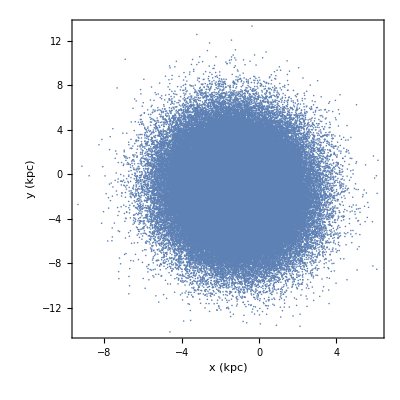

```mathematica
ListPlot[dmCords00xy, FrameLabel->{"x (kpc)","y (kpc)"}, Axes->True, Frame->True, FrameStyle->Directive[Thickness[0.003],FontSize->15,FontFamily->"Times"],FrameTicksStyle->Directive[Black, 15], LabelStyle->Directive[14], AspectRatio->1]
closeCellGroup[]
```

```mathematica
Timing[dmCords00xz=dmCords00RV⟦All,{1,3}⟧;]
```

{0.,Null}

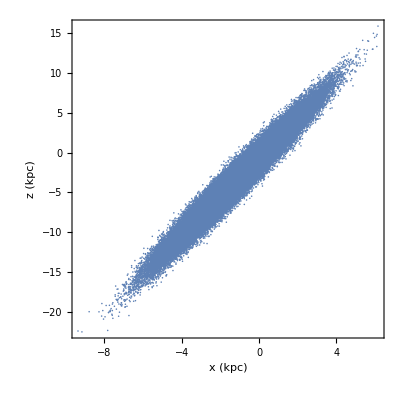

```mathematica
ListPlot[dmCords00xz, FrameLabel->{"x (kpc)","z (kpc)"}, Axes->True, Frame->True, FrameStyle->Directive[Thickness[0.003],FontSize->15,FontFamily->"Times"],FrameTicksStyle->Directive[Black, 15], LabelStyle->Directive[14], AspectRatio->1]
closeCellGroup[]
```

## Create example data sets

```mathematica
closeCellGroup[] := (SelectionMove[EvaluationCell[], Next,Cell]; 
FrontEndExecute[FrontEndToken["SelectionCloseUnselectedCells"]])
```

```mathematica
simuationSize=168357;
```

I use the displayed values in your original notebook to estimate the distribution characteristics of your variables in order to simulate similar sized datasets.  There are only 6 values each for the coordinate and velocity sample distributions and 76 values for the LMC tag data.  I use Mathematica’s “EstimatedDistribution” function and assume that the generating processes for both the coordinates and the velocities are approximated by a Multivariate Normal Distribution.  Then I use the estimated mean vectors and covariance matrices to simulate 168,357 data points.  I then  use “FindDistributionParameters to see determine the mean vectors and covariance matrices of the simulated data.  Of course this is crude.  But it allows me to test my code suggestions against datasets of the same size.

For the LMC tag data, I used your analysis to generate a vector of {-1 and 1} to weighted to produce the same percentage of LMC particles in the same sized vector.

I use the closeCellGroup[] function above to close the code cells that estimate the sample distribution values and generate the simulated datasets.  This allows the output to appear less cluttered and keeps the utility code out of the way.  To see the code, simply double click on the enclosing cell brackets.

### DM coordinate variables

Notebook data

```mathematica
MatrixForm[dmCords00={{0.016431426629424095,-0.1076788678765297,0.03446260467171669},{-0.08331732451915741,-0.005956035573035479,0.18741817772388458},{0.23650655150413513,0.05569346994161606,0.0347386933863163},{-4.803868293762207,0.7528245449066162,-11.71234130859375},{-1.302531123161316,-8.16396427154541,-4.614678382873535},{-1.0871785879135132,-0.7993932962417603,-4.996247291564941}}]
closeCellGroup[]
```

(0.0164314 | -0.107679 | 0.0344626
-0.0833173 | -0.00595604 | 0.187418
0.236507 | 0.0556935 | 0.0347387
-4.80387 | 0.752825 | -11.7123
-1.30253 | -8.16396 | -4.61468
-1.08718 | -0.799393 | -4.99625)

Estimated sample data distribution parameters

```mathematica
edistCoords=EstimatedDistribution[dmCords00, MultinormalDistribution[Array[μ,3],Array[s,{3,3}]]]
```

MultinormalDistribution[{-1.17066,-1.37808,-3.51111},{{2.96603,-0.296873,7.17307},{-0.296873,9.4127,0.63605},{7.17307,0.63605,18.2512}}]

Multivariate Normal mean and covariance from simulated data

```mathematica
dmCords00RV=RandomVariate[edistCoords,simuationSize];
fdistpar=FindDistributionParameters[dmCords00RV, MultinormalDistribution[Array[μ,3],Array[s,{3,3}]]]
```

{μ[1]→-1.16896,μ[2]→-1.37395,μ[3]→-3.50594,s[1,1]→2.95818,s[1,2]→-0.297792,s[1,3]→7.15185,s[2,1]→-0.297792,s[2,2]→9.3484,s[2,3]→0.637228,s[3,1]→7.15185,s[3,2]→0.637228,s[3,3]→18.1951}

### DM velocity variables

Notebook data

```mathematica
MatrixForm[dmVels00={{36.43170166015625,-9.138969421386719,-26.757831573486328},{-24.890954971313477,-21.605627059936523,-3.0834414958953857},{-9.940251350402832,-14.906100273132324,33.107540130615234},{-169.15914916992188,139.89755249023438,-290.9612121582031},{-104.96575164794922,120.04015350341797,-352.1723937988281},{-103.65585327148438,-1.9502073526382446,-415.2244873046875}}]
Dimensions@%
closeCellGroup[]
```

(36.4317 | -9.13897 | -26.7578
-24.891 | -21.6056 | -3.08344
-9.94025 | -14.9061 | 33.1075
-169.159 | 139.898 | -290.961
-104.966 | 120.04 | -352.172
-103.656 | -1.95021 | -415.224)

{6,3}

Estimated sample data distribution parameters

```mathematica
edist=EstimatedDistribution[dmVels00, MultinormalDistribution[Array[μ,3],Array[s,{3,3}]]]
```

MultinormalDistribution[{-62.6967,35.3895,-175.849},{{4806.26,-3732.85,10307.9},{-3732.85,4540.47,-7502.17},{10307.9,-7502.17,32896.7}}]

Multivariate Normal mean and covariance from simulated data

```mathematica
dmVels00RV=RandomVariate[edist,simuationSize];
fdistpar=FindDistributionParameters[dmVels00RV, MultinormalDistribution[Array[μ,3],Array[s,{3,3}]]]
```

{μ[1]→-62.4459,μ[2]→35.2869,μ[3]→-175.533,s[1,1]→4821.1,s[1,2]→-3729.1,s[1,3]→10337.,s[2,1]→-3729.1,s[2,2]→4531.54,s[2,3]→-7492.83,s[3,1]→10337.,s[3,2]→-7492.83,s[3,3]→32860.4}

### LMC_tag for each DM particle variable

```mathematica
Notebook data
```

```mathematica
dmTag00={-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.};
Length@dmTag00
closeCellGroup[]
```

76

Simulated LMC tag data

```mathematica
dmTag00RV=RandomChoice[{.17,1-.17}->{-1,1},simuationSize];
Length@dmTag00RV
```

168357

```mathematica
generatedData={dmCords00RV,dmVels00RV,dmTag00RV};
```